```mathematica
<<SpinorHelicity6D`
```

===============SpinorHelicity6D================

Authors: Manuel Accettulli Huber (QMUL)

Stefano De Angelis (QMUL)

Please report any bug to:

m.accettullihuber@qmul.ac.uk

s.deangelis@qmul.ac.uk

Version 1.2 , last update 16/04/2020

===============================================

### Rodolfo’s version

```mathematica
(*(* Rules for Schouten simplification *)
SchoutenRules =
    {k_. SpinorAngleBracket[a_,c_] SpinorAngleBracket[b_,d_] - k_. SpinorAngleBracket[a_,d_] SpinorAngleBracket[b_,c_] :> k SpinorAngleBracket[a,b] SpinorAngleBracket[c,d],
     k_. SpinorAngleBracket[a_,b_] SpinorAngleBracket[c_,d_] + k_. SpinorAngleBracket[a_,d_] SpinorAngleBracket[b_,c_] :> k SpinorAngleBracket[a,c] SpinorAngleBracket[b,d],
     k_. SpinorAngleBracket[a_,c_] SpinorAngleBracket[b_,d_] - k_. SpinorAngleBracket[a_,b_] SpinorAngleBracket[c_,d_] :> k SpinorAngleBracket[a,d] SpinorAngleBracket[b,c],
     k_. SpinorSquareBracket[a_,c_] SpinorSquareBracket[b_,d_] - k_. SpinorSquareBracket[a_,d_] SpinorSquareBracket[b_,c_] :> k SpinorSquareBracket[a,b] SpinorSquareBracket[c,d],
     k_. SpinorSquareBracket[a_,b_] SpinorSquareBracket[c_,d_] + k_. SpinorSquareBracket[a_,d_] SpinorSquareBracket[b_,c_] :> k SpinorSquareBracket[a,c] SpinorSquareBracket[b,d],
     k_. SpinorSquareBracket[a_,c_] SpinorSquareBracket[b_,d_] - k_. SpinorSquareBracket[a_,b_] SpinorSquareBracket[c_,d_] :> k SpinorSquareBracket[a,d] SpinorSquareBracket[b,c]}

(* Generates all possibile Schouten identities associated with a given set of momenta. *)
SchoutenIdentities[momenta_List] :=
    ({a,b,c,d} ↦
        Sequence@@
            {SpinorAngleBracket[a,b] SpinorAngleBracket[c,d] + SpinorAngleBracket[b,c] SpinorAngleBracket[a,d] + SpinorAngleBracket[c,a] SpinorAngleBracket[b,d] == 0,
             SpinorSquareBracket[a,b] SpinorSquareBracket[c,d] + SpinorSquareBracket[b,c] SpinorSquareBracket[a,d] + SpinorSquareBracket[c,a] SpinorSquareBracket[b,d] == 0})@@@
        Subsets[momenta,{4}]

(* SchoutenSimplify*)
SchoutenSimplify[expr_] :=
    Simplify[expr,
        Assumptions -> SchoutenIdentities[Momenta[expr]],
        TransformationFunctions -> {Automatic, (e ↦ e /. SchoutenRules)}]*)
```

## Experimenting with Mathematica’s Simplify

### Simple expressions with Plus and Times

```mathematica
Simplify[a+b+c+d,Assumptions->a+b==c]
```

a+b+c+d

```mathematica
(*The simplification does not occur because for Mathematica it is not a simplification at all! Compare the fullforms and remember that the default ComplexityFunction is essentially a LeafCount with some additional penalty for huge integers*)
```

```mathematica
LeafCount[a+b+c+d]
```

5

```mathematica
LeafCount[2*c+d]
```

5

```mathematica
a+b+c+d//FullForm
```

Plus[a,b,c,d]

```mathematica
2*c+d//FullForm
```

Plus[Times[2,c],d]

```mathematica
LeafCount[a+2*b+c+d+e]
```

8

```mathematica
LeafCount[b+2*c+d+e]
```

7

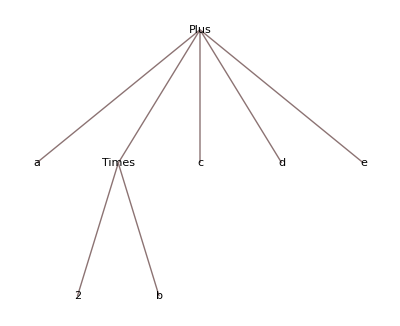

```mathematica
TreeForm[a+2*b+c+d+e]
```

```mathematica
Level[a+2*b+c+d+e,1]
```

{a,2 b,c,d,e}

```mathematica
Level[a+2*b+c+d+e,2]
```

{a,2,b,2 b,c,d,e}

```mathematica
Level[a+2*b+c+d+e,3]
```

{a,2,b,2 b,c,d,e}

```mathematica
Level[a+2*b+c+d+e,-1]
```

{a,2,b,2 b,c,d,e}

```mathematica
Level[a+2*b+c+d+e,-2]
```

{2 b}

```mathematica
Level[a+2*b+c+d+e,-3]
```

{}

```mathematica
Count[a+2*b+c+d+e//FullForm,_Plus]
```

1

```mathematica
Count[a+2*b+c+3*(d+e)//FullForm,_Plus,Infinity]
```

2

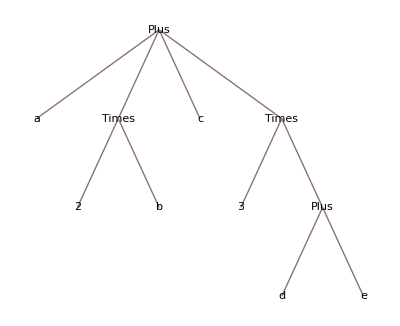

```mathematica
a+2*b+c+3*(d+e)//TreeForm
```

```mathematica
Count[a+2*b+c+3*(d+e*(f+h)),_Plus,Infinity]
```

2

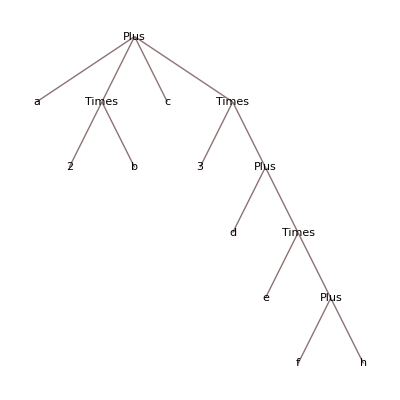

```mathematica
a+2*b+c+3*(d+e*(f+h))//TreeForm
```

```mathematica
Count[a+2*b+c+3*(d+e*(f+h)),_Plus,Infinity]//RepeatedTiming
Count[a+2*b+c+3*(d+e*(f+h))//FullForm,_Plus,Infinity]//RepeatedTiming
```

{1.68×10^-6,2}

{3.×10^-6,3}

```mathematica
(*Testing the speed of FullForm*)
```

```mathematica
test[x_]:=a[x]+x*b[x]
```

```mathematica
Count[Nest[test,x,8]//FullForm,_Plus,Infinity]//RepeatedTiming
```

{0.001,3280}

```mathematica
Count[Nest[test,x,8],_Plus,Infinity]//RepeatedTiming
```

{0.001,3279}

```mathematica
Nest[test,x,8]//LeafCount//AbsoluteTiming
```

{0.000376,19681}

```mathematica
(*It seems that there ia almost no speed difference and when there is using FullForm is actually faster*)
```

### Playing with powers

```mathematica
LeafCount[a^7*b^5]
```

7

```mathematica
Simplify[a^7*b^5,Assumptions->a^3*b^3==1]
```

a^4 b^2

```mathematica
LeafCount[a^4*b^2]
```

7

```mathematica
(*So even if from a leafcount perspective the initial and final expression are the same Mathematica is mart enough to regognize that smaller powers are better*)
```

### My first complexity function

```mathematica
(*First lesson from above: I like Times better than Plus, but Mathematica does not. So lets try and see what happens if we make the Plus more expensive*)
```

```mathematica
MyComplexityFunction[exp_]:=Module[{complexity},
(*Take Mathematica's LeafCount as a reference and add penalties for every Plus in the expression. Assign weight 2 to Plus instead of one.*)
complexity=LeafCount[exp];
complexity=complexity+Count[exp//FullForm,_Plus,Infinity];
Return[complexity];
];
```

### Test

```mathematica
Simplify[a+b+c+d,Assumptions->a+b==c]
```

a+b+c+d

```mathematica
Simplify[a+b+c+d,Assumptions->a+b==c,ComplexityFunction->MyComplexityFunction]
```

2 c+d

### Look at spinors

```mathematica
12 23//LeafCount
```

7

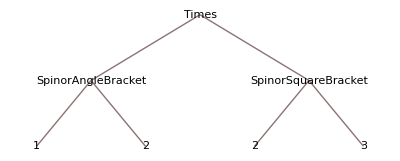

```mathematica
12 23//TreeForm
```

```mathematica
p1p2 p2p3//ToChain//LeafCount
```

7

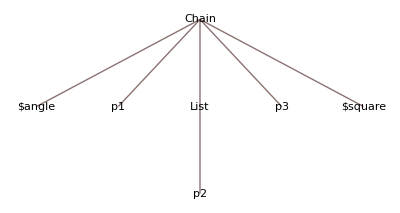

```mathematica
p1p2 p2p3//ToChain//TreeForm
```

```mathematica
(*Assume you have conserved external momenta and you want to simplify the following:*)
```

```mathematica
exp=p1p3 p3p2-p1p4 p4p2
```

-p1p3 p2p3+p1p4 p2p4

```mathematica
exp//ToChain
```

p1{p3}p2-p1{p4}p2

```mathematica
(*We want to apply momentum conservation to the chains*)
```

```mathematica
DeclareMom[p1,p2,p3,p4]
```

```mathematica
Simplify[exp,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}]},ComplexityFunction->MyComplexityFunction]
```

-p1p3 p2p3+p1p4 p2p4

```mathematica
ChainSimplify[exp//ToChain,{MomCon->{p4->-p3-p1-p2}}]
```

2 p1{p3}p2

```mathematica
%//LeafCount
```

9

```mathematica
exp//LeafCount
```

16

```mathematica
(*Chains are far more expensive than brackets, so we have to depenalise them*)
```

### Second complexity function

```mathematica
MyComplexityFunction[exp_]:=Module[{complexity,fullexp},
(*Take Mathematica's LeafCount as a reference and add penalties for every Plus in the expression.*)

(*Assign weight 2 to Plus instead of one.*)
(*Chains get a bonus -3*)
fullexp=exp//FullForm;
complexity=LeafCount[exp]+Count[fullexp,_Plus,Infinity]-3*Count[fullexp,_Chain,Infinity];
Return[complexity];
];
```

```mathematica
DeclareMom[p1,p2,p3,p4]
```

```mathematica
KillMasses[{p1,p2,p3,p4}]
```

```mathematica
Simplify[exp//ToChain,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainToSpinor[e]},ComplexityFunction->MyComplexityFunction]
```

2 p1{p3}p2

```mathematica
%//MyComplexityFunction
```

6

```mathematica
%%//ChainToSpinor//MyComplexityFunction
```

8

```mathematica
(*But I like my expressions split up into spinors so let us try weighting the chains just slightly more that the angle and square brackets*)
```

```mathematica
MyComplexityFunction[exp_]:=Module[{complexity,fullexp},
(*Take Mathematica's LeafCount as a reference and add penalties for every Plus in the expression.*)

(*Assign weight 2 to Plus instead of one.*)
(*Chains get a bonus -2*)
fullexp=exp//FullForm;
complexity=LeafCount[exp]+Count[fullexp,_Plus,Infinity]-2*Count[fullexp,_Chain,Infinity];
Return[complexity];
];
```

```mathematica
Simplify[exp//ToChain,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainToSpinor[e]},ComplexityFunction->MyComplexityFunction]
```

2 p1{p3}p2

```mathematica
%//MyComplexityFunction
```

7

```mathematica
%%//ChainToSpinor//MyComplexityFunction
```

8

```mathematica
(*The problem is that the a single chain will always be favoured with respect to a multiple brackets. And if they would not be favoured you would not get the replacement in the first place*)
```

```mathematica
(*Let's see if it still works even if we do not apply only the right momentum conservation but give him multiple options*)
```

```mathematica
exp
```

-p1p3 p2p3+p1p4 p2p4

```mathematica
Simplify[exp//ToChain,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p3->-p4-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p2->-p3-p1-p4}}],e↦ChainSimplify[e,{MomCon->{p1->-p3-p4-p2}}]},ComplexityFunction->MyComplexityFunction]
```

-2 p1{p4}p2

```mathematica
%//ChainToSpinor
```

2 p1p4 p2p4

```mathematica
(*What if conversion to spinors supersimplifies everything?*)
```

```mathematica
exp=(-p1p3 p2p3+p1p4 p2p4)/(p1p4 p4p2)
```

-(-p1p3 p2p3+p1p4 p2p4)/(p1p4 p2p4)

```mathematica
Simplify[exp//ToChain,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p3->-p4-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p2->-p3-p1-p4}}],e↦ChainSimplify[e,{MomCon->{p1->-p3-p4-p2}}],e↦ChainToSpinor[e]},ComplexityFunction->MyComplexityFunction]
```

-2

```mathematica
(*It fu--ing works!!!!!*)
```

```mathematica
exp=(-p1p3 p2p3+p1p4 p2p4)/(p1p3 p3p2)
```

-(-p1p3 p2p3+p1p4 p2p4)/(p1p3 p2p3)

```mathematica
Simplify[exp//ToChain,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p3->-p4-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p2->-p3-p1-p4}}],e↦ChainSimplify[e,{MomCon->{p1->-p3-p4-p2}}],e↦ChainToSpinor[e]},ComplexityFunction->MyComplexityFunction]
```

2

```mathematica
exp=(-p1p3 p2p3+p1p4 p2p4)/(p1p3 p3p2)+p1p2 p3p4+p1p2 p2p4
```

p1p2 p2p4-(-p1p3 p2p3+p1p4 p2p4)/(p1p3 p2p3)+p1p2 p3p4

```mathematica
Simplify[exp//ToChain,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p3->-p4-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p2->-p3-p1-p4}}],e↦ChainSimplify[e,{MomCon->{p1->-p3-p4-p2}}],e↦ChainToSpinor[e]},ComplexityFunction->MyComplexityFunction]
```

2+p1{p2}p4+p1p2 p3p4

```mathematica
Simplify[exp,TransformationFunctions->{Automatic,e↦ToChain[e], e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p3->-p4-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p2->-p3-p1-p4}}],e↦ChainSimplify[e,{MomCon->{p1->-p3-p4-p2}}],e↦ChainToSpinor[e]},ComplexityFunction->MyComplexityFunction]
```

2+p1{p2}p4+p1p2 p3p4

```mathematica
exp//Simplify
```

1-(p1p4 p2p4)/(p1p3 p2p3)+p1p2 (p2p4+p3p4)

```mathematica
Simplify[%//ToChain,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p3->-p4-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p2->-p3-p1-p4}}],e↦ChainSimplify[e,{MomCon->{p1->-p3-p4-p2}}],e↦ChainToSpinor[e]},ComplexityFunction->MyComplexityFunction]
```

2+p1{p2}p4+p1p2 p3p4

```mathematica
exp=(-p1p3 p2p3+p1p4 p2p4)/(p1p3 p3p2)+(-p3p1 p4p1+p3p2 p4p2)/(p3p1 p1p4)
```

-(-p1p3 p2p3+p1p4 p2p4)/(p1p3 p2p3)-(-p1p3 p1p4+p2p3 p2p4)/(p1p3 p1p4)

```mathematica
Simplify[exp,TransformationFunctions->{Automatic,e↦ChainSimplify[e,{MomCon->{p4->-p3-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p3->-p4-p1-p2}}],e↦ChainSimplify[e,{MomCon->{p2->-p3-p1-p4}}],e↦ChainSimplify[e,{MomCon->{p1->-p3-p4-p2}}],e↦ChainToSpinor[e],e ↦ ToChain[e]},ComplexityFunction->MyComplexityFunction]
```

4

### Most up to date complexity function

```mathematica
MyComplexityFunction[exp_]:=Module[{complexity,fullexp},
(*Take Mathematica's LeafCount as a reference and add penalties for every Plus in the expression.*)

(*Assign weight 2 to Plus instead of one.*)
(*Chains get a bonus -2*)
fullexp=exp//FullForm;
complexity=LeafCount[exp]+Count[fullexp,_Plus,Infinity]-2*Count[fullexp,_Chain,Infinity];
Return[complexity];
];
```

### SpinorSimplify

(*Notice that we set ReduceComplete to False, might be relevant later on. Also we still have to take scalar products and S4 into account*)

```mathematica
SpinorSimplify[exp_,MomConservation_]:=Module[{momcon,mom,momlist,transformationfunctions,locexp},
(*First we build all the replacements which are given by momentum conservation.*)

(*Exract all the momenta present in the relations*)
momlist={};
mom[x_]:=If[MemberQ[momlist,x],x,AppendTo[momlist,x];x];
momcon=Flatten[{MomConservation}/.{A_/;MemberQ[MomList,A]:>mom[A],Rule->Equal,RuleDelayed->Equal}];

(*Generate Chainsimplify with each single momentum conservation relation applied.*)
transformationfunctions={};
Do[transformationfunctions={transformationfunctions,Solve[i,j]},{i,momcon},{j,momlist}];
transformationfunctions=Table[With[{j=i},e ↦ChainSimplify[e,{MomCon->{j},ReduceComplete->False}]],{i,Flatten[transformationfunctions]}];

(*Now add the functions which transform backa and forth among Chains and spinor brackets as well as the automatic functions*)
transformationfunctions={Automatic,e ↦ ToChain[e],e ↦ ChainToSpinor[e],transformationfunctions}//Flatten;

(*Now apply the simplification using the custom ComplexityFunction*)

locexp=Simplify[exp,ComplexityFunction->MyComplexityFunction,TransformationFunctions->transformationfunctions,Trig->False];

Return[locexp];
];
```

```mathematica
MomList
```

{}

```mathematica
DeclareMom[l1,l2]
```

```mathematica
exp
```

exp

```mathematica
SpinorSimplify[exp,{p1+p2+p3+p4->0}]
```

exp

```mathematica
SpinorSimplify[exp,{l1+l2+p1+p2->0,l1+l2->p3+p4,p1+p2+p3+p4->0}]
```

exp

### SchoutenSimplify, to be fixed...

```mathematica
exp=p1p2 p3p4+p1p3 p4p2
```

-p1p3 p2p4+p1p2 p3p4

```mathematica
exp//SchoutenSimplify
```

-p1p4 p2p3

```mathematica
Simplify[exp,TransformationFunctions->{Automatic,e ↦ e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]},e ↦ e/.{SpinorSquareBracket[x_,y_]*SpinorSquareBracket[z_,k_]:>-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z]}}]
```

-p1p4 p2p3

```mathematica
(*It seems incredibly easy to implement despite what Rodolfo did...*)
```

```mathematica
SchoutenSimplify2[exp_]:=Simplify[exp,TransformationFunctions->{Automatic,e ↦ e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]},e ↦ e/.{SpinorSquareBracket[x_,y_]*SpinorSquareBracket[z_,k_]:>-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z]}}]
```

```mathematica
exp//SchoutenSimplify2
```

-p1p4 p2p3

```mathematica
exp=(p1p2 p3p4+p1p3 p4p2)*p1p2//Expand
```

-p1p2 p1p3 p2p4+p1p2^2 p3p4

```mathematica
exp//SchoutenSimplify2
```

-p1p2 p1p4 p2p3

```mathematica
(*This does actually not work with powers...*)
```

```mathematica
14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2;
%//SchoutenSimplify2
%%//SchoutenSimplify
```

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

3 13^2 24^2-12 13 24 34+12^2 34^2

### SpinorSimplify with Schouten

```mathematica
(*Wrong version*)
```

```mathematica
SpinorSimplify[exp_,MomConservation_:{}]:=Module[{momcon,mom,momlist,transformationfunctions,locexp,schouten},

If[MomConservation==={},
locexp=SchoutenSimplify[exp];
Return[locexp],
(*First we build all the replacements which are given by momentum conservation.*)

(*Exract all the momenta present in the relations*)
momlist={};
mom[x_]:=If[MemberQ[momlist,x],x,AppendTo[momlist,x];x];
momcon=Flatten[{MomConservation}/.{A_/;MemberQ[MomList,A]:>mom[A],Rule->Equal,RuleDelayed->Equal}];

(*Generate Chainsimplify with each single momentum conservation relation applied.*)
transformationfunctions={};
Do[transformationfunctions={transformationfunctions,Solve[i,j]},{i,momcon},{j,momlist}];
transformationfunctions=Table[With[{j=i},e ↦ChainSimplify[e,{MomCon->{j},ReduceComplete->False}]],{i,Flatten[transformationfunctions]}];

(*Schouten identities*)
schouten={e ↦ e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]},e ↦ e/.{SpinorSquareBracket[x_,y_]*SpinorSquareBracket[z_,k_]:>-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z]}};

(*Now add the functions which transform backa and forth among Chains and spinor brackets as well as the automatic functions and Schouten identities*)
transformationfunctions={Automatic,e ↦ ToChain[e],e ↦ ChainToSpinor[e],schouten,transformationfunctions}//Flatten;

(*Now apply the simplification using the custom ComplexityFunction*)

locexp=Simplify[exp,ComplexityFunction->MyComplexityFunction,TransformationFunctions->transformationfunctions,Trig->False];

Return[locexp];

];

];
```

```mathematica
(*Corrected version*)
```

```mathematica
Clear[SpinorSimplify]
```

```mathematica
SpinorSimplify[exp_,MomConservation_:{}]:=Module[{momcon,mom,momlist,transformationfunctions,locexp,schouten},

If[MomConservation==={},
transformationfunctions={};
,
(*First we build all the replacements which are given by momentum conservation.*)

(*Exract all the momenta present in the relations*)
momlist={};
mom[x_]:=If[MemberQ[momlist,x],x,AppendTo[momlist,x];x];
momcon=Flatten[{MomConservation}/.{A_/;MemberQ[MomList,A]:>mom[A],Rule->Equal,RuleDelayed->Equal}];

(*Generate Chainsimplify with each single momentum conservation relation applied.*)
transformationfunctions={};
Do[transformationfunctions={transformationfunctions,Solve[i,j]},{i,momcon},{j,momlist}];
transformationfunctions=Table[With[{j=i},e ↦ChainSimplify[e,{MomCon->{j},ReduceComplete->False}]],{i,Flatten[transformationfunctions]}];

];

(*Schouten identities*)
schouten={e ↦ e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]},e ↦ e/.{SpinorSquareBracket[x_,y_]*SpinorSquareBracket[z_,k_]:>-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z]}};

(*Now add the functions which transform back and forth among Chains and spinor brackets as well as the automatic functions and Schouten identities*)
transformationfunctions={Automatic,e ↦ ToChain[e],e ↦ ChainToSpinor[e],schouten,transformationfunctions}//Flatten;

(*Now apply the simplification using the custom ComplexityFunction*)

locexp=Simplify[exp,ComplexityFunction->MyComplexityFunction,TransformationFunctions->transformationfunctions,Trig->False];

Return[locexp];

];
```

### Something to sort out.

#### First problem. Sorted

```mathematica
12 34+13 42//SpinorSimplify
```

-14 23

```mathematica
DeclareMom[p1,p2,p3]
```

```mathematica
KillMasses[p1,p2,p3]
```

```mathematica
test=p1p2/(p1{p2}p3)
```

p1p2/(p1{p2}p3)

```mathematica
test//SpinorSimplify
```

p1p2/(p1{p2}p3)

```mathematica
(*It does not simplify despite the single operation needed...*)
```

```mathematica
Simplify[test,ComplexityFunction->MyComplexityFunction,TransformationFunctions->{Automatic,e ↦ ChainToSpinor[e]}]
```

1/p2p3

```mathematica
Clear[SpinorSimplify]
```

```mathematica
SpinorSimplify[exp_,MomConservation_:{}]:=Module[{momcon,mom,momlist,transformationfunctions,locexp,schouten},

If[MomConservation==={},
transformationfunctions={};
,
(*First we build all the replacements which are given by momentum conservation.*)

(*Exract all the momenta present in the relations*)
momlist={};
mom[x_]:=If[MemberQ[momlist,x],x,AppendTo[momlist,x];x];
momcon=Flatten[{MomConservation}/.{A_/;MemberQ[MomList,A]:>mom[A],Rule->Equal,RuleDelayed->Equal}];

(*Generate Chainsimplify with each single momentum conservation relation applied.*)
transformationfunctions={};
Do[transformationfunctions={transformationfunctions,Solve[i,j]},{i,momcon},{j,momlist}];
transformationfunctions=Table[With[{j=i},e ↦ChainSimplify[e,{MomCon->{j},ReduceComplete->False}]],{i,Flatten[transformationfunctions]}];

];

(*Schouten identities*)
schouten={e ↦ e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]},e ↦ e/.{SpinorSquareBracket[x_,y_]*SpinorSquareBracket[z_,k_]:>-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z]}};

(*Now add the functions which transform back and forth among Chains and spinor brackets as well as the automatic functions and Schouten identities*)
transformationfunctions={Automatic,e ↦ ToChain[e],e ↦ ChainToSpinor[e],schouten,transformationfunctions}//Flatten;

(*Now apply the simplification using the custom ComplexityFunction*)

locexp=Simplify[exp,ComplexityFunction->MyComplexityFunction,TransformationFunctions->transformationfunctions,Trig->False];

Return[locexp];

];
```

```mathematica
test//SpinorSimplify
```

{Automatic,Function[e,ToChain[e]],Function[e,ChainToSpinor[e]],Function[e,e/.{x_y_ z_k_:>-xz ky-xk yz}],Function[e,e/.{x_y_ z_k_:>-xz ky-xk yz}]}

1/p2p3

```mathematica
SpinorSimplify[test,p1->-p2-p3-p4]
```

{Automatic,Function[e,ToChain[e]],Function[e,ChainToSpinor[e]],Function[e,e/.{x_y_ z_k_:>-xz ky-xk yz}],Function[e,e/.{x_y_ z_k_:>-xz ky-xk yz}],Function[e$,ChainSimplify[e$,{MomCon→{p1→-p2-p3-p4},ReduceComplete→False}]],Function[e$,ChainSimplify[e$,{MomCon→{p2→-p1-p3-p4},ReduceComplete→False}]],Function[e$,ChainSimplify[e$,{MomCon→{p3→-p1-p2-p4},ReduceComplete→False}]]}

1/p2p3

#### Second problem

```mathematica
Clear[SpinorSimplify]
```

```mathematica
SpinorSimplify[exp_,MomConservation_:{}]:=Module[{momcon,mom,momlist,transformationfunctions,locexp,schouten},

If[MomConservation==={},
transformationfunctions={};
,
(*First we build all the replacements which are given by momentum conservation.*)

(*Exract all the momenta present in the relations*)
momlist={};
mom[x_]:=If[MemberQ[momlist,x],x,AppendTo[momlist,x];x];
momcon=Flatten[{MomConservation}/.{A_/;MemberQ[MomList,A]:>mom[A],Rule->Equal,RuleDelayed->Equal}];

(*Generate Chainsimplify with each single momentum conservation relation applied.*)
transformationfunctions={};
Do[transformationfunctions={transformationfunctions,Solve[i,j]},{i,momcon},{j,momlist}];
transformationfunctions=Table[With[{j=i},e ↦ChainSimplify[e,{MomCon->{j},ReduceComplete->False}]],{i,Flatten[transformationfunctions]}];

];

(*Schouten identities*)
schouten={e ↦ e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]},e ↦ e/.{SpinorSquareBracket[x_,y_]*SpinorSquareBracket[z_,k_]:>-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z]}};

(*Now add the functions which transform back and forth among Chains and spinor brackets as well as the automatic functions and Schouten identities*)
transformationfunctions={Automatic,e ↦ ToChain[e],e ↦ ChainToSpinor[e],schouten,transformationfunctions}//Flatten;

Print[transformationfunctions];
(*Now apply the simplification using the custom ComplexityFunction*)

locexp=Simplify[exp,ComplexityFunction->MyComplexityFunction,TransformationFunctions->transformationfunctions,Trig->False];

Return[locexp];

];
```

```mathematica
test=p1p2/(p1{p4}p3)
```

p1p2/(p1{p4}p3)

```mathematica
SpinorSimplify[test,p1->-p2-p3-p4]
```

{Automatic,Function[e,ToChain[e]],Function[e,ChainToSpinor[e]],Function[e,e/.{x_y_ z_k_:>-xz ky-xk yz}],Function[e,e/.{x_y_ z_k_:>-xz ky-xk yz}],Function[e$,ChainSimplify[e$,{MomCon→{p1→-p2-p3-p4},ReduceComplete→False}]],Function[e$,ChainSimplify[e$,{MomCon→{p2→-p1-p3-p4},ReduceComplete→False}]],Function[e$,ChainSimplify[e$,{MomCon→{p3→-p1-p2-p4},ReduceComplete→False}]],Function[e$,ChainSimplify[e$,{MomCon→{p4→-p1-p2-p3},ReduceComplete→False}]]}

p1p2/(p1{p4}p3)

```mathematica
1/test
```

(p1{p4}p3)/p1p2

```mathematica
Simplify[1/test,ComplexityFunction->MyComplexityFunction,TransformationFunctions->{Automatic,e ↦ ChainSimplify[e,{MomCon->p4->-p1-p2-p3}],e ↦ ChainToSpinor[e],e ↦ ToChain[e]}]
```

(p1{p4}p3)/p1p2

```mathematica
(*It seems Mathematica does not want to apply momentum conservation and then break the chain to spinors, why? Maybe because a minus appears increasing intermediate complexity despite the overall complexity would decrease in the end.*)
```

```mathematica
MomList
```

{p1,p2,p3,p4}

```mathematica
ChainSimplify[test,{MomCon->p4->-p1-p2-p3}]
```

-p1p2/(p1{p2}p3)

```mathematica
(*Analogous case but simpler*)
```

```mathematica
test=(a+b)/c
```

(a+b)/c

```mathematica
Simplify[test,TransformationFunctions->{exp ↦exp/.{c->d-e},exp ↦exp/.{e->d-a-b}}]
```

(a+b)/c

```mathematica
test/.{c->d-e}
%/.{e->d-a-b}
```

(a+b)/(d-e)

1

```mathematica
(*Whenever the intermediate expression is more complicated the simplification does not happen.*)
```

#### Trying a new complexity functions

```mathematica
ComplicatedComplexityFunction[exp_,list_]:=LeafCount[Simplify[exp,TransformationFunctions->list]]
```

```mathematica
ComplicatedComplexityFunction[exp_,list_]:=Module[{loc1,count},
count=LeafCount[loc1=Simplify[exp,TransformationFunctions->list]];
Print["input ",exp];
Print["manipulated ", loc1];
Print["count ",count];
Return[count]
];
```

```mathematica
OptionValue[Simplify,TransformationFunctions]
```

```mathematica
test=(a+b)/c
```

(a+b)/c

```mathematica
Simplify[test,TransformationFunctions->{exp ↦exp/.{c->d-e},exp ↦exp/.{e->d-a-b}},ComplexityFunction->(ComplicatedComplexityFunction[#,{exp ↦exp/.{c->d-e},exp ↦exp/.{e->d-a-b}}]&)]
```

input (a+b)/c

manipulated (a+b)/c

count 7

input (a+b)/c

manipulated (a+b)/c

count 7

input (a+b)/(d-e)

manipulated 1

count 1

input (a+b)/(d-e)

manipulated 1

count 1

input 1

manipulated 1

count 1

input (a+b)/(d-e)

manipulated 1

count 1

input a+b

manipulated a+b

count 3

input a+b

manipulated a+b

count 3

input a+b

manipulated a+b

count 3

input a

manipulated a

count 1

input a

manipulated a

count 1

input a

manipulated a

count 1

input b

manipulated b

count 1

input b

manipulated b

count 1

input b

manipulated b

count 1

input a+b

manipulated a+b

count 3

input 1/(d-e)

manipulated 1/(a+b)

count 5

input 1/(a+b)

manipulated 1/(a+b)

count 5

input 1/(d-e)

manipulated 1/(a+b)

count 5

input d-e

manipulated a+b

count 3

input a+b

manipulated a+b

count 3

input d-e

manipulated a+b

count 3

input d

manipulated d

count 1

input d

manipulated d

count 1

input d

manipulated d

count 1

input -e

manipulated -e

count 3

input a+b-d

manipulated a+b-d

count 6

input -e

manipulated -e

count 3

input -1

manipulated -1

count 1

input -1

manipulated -1

count 1

input -1

manipulated -1

count 1

input e

manipulated e

count 1

input -a-b+d

manipulated -a-b+d

count 8

input e

manipulated e

count 1

input -e

manipulated -e

count 3

input d-e

manipulated a+b

count 3

input -1

manipulated -1

count 1

input -1

manipulated -1

count 1

input -1

manipulated -1

count 1

input 1/(d-e)

manipulated 1/(a+b)

count 5

input (a+b)/(d-e)

manipulated 1

count 1

(a+b)/(d-e)

## Some tests to be carried out...

### R^3 helicity flip in a given channel

### BCFW 4 pt

```mathematica
(*4pt, +--+, with 1 and 4 shifted*)
```

```mathematica
bcfw=(p1hatPhat^3*-Phatp3^3)/(p2Phat p1hatp2 S4[p1,p2]p3p4hat p4hat-Phat)+(p2Phat^3*p4hat-Phat^3)/(Phatp1hat p1hatp2 S4[p1,p2]-Phatp3 p3p4hat)
```

(p3Phat^3 p1hatPhat^3)/(S4[p1,p2] p3p4hat p4hatPhat p1hatp2 p2Phat)-(p2Phat^3 p4hatPhat^3)/(S4[p1,p2] p1hatp2 p1hatPhat p3p4hat p3Phat)

```mathematica
HelicityWeight[bcfw]
```

{{p1hat,2},{p2,-2},{p3,-2},{p4hat,2}}

```mathematica
bcfw=SpinorReplace[bcfw,{p1hat->p1+z*p4,p4hat->p4,p1hat->p1,p4hat->p4-z*p1}]
```

(p3Phat^3 p1Phat^3)/(S4[p1,p2] p3p4 p4Phat p1p2 p2Phat)-(p2Phat^3 (-z p1Phat+p4Phat)^3)/(S4[p1,p2] (p1p2-z p2p4) (p1Phat+z p4Phat) (z p1p3+p3p4) p3Phat)

```mathematica
DeclareMom[Phat,P]
```

```mathematica
SpinorSimplify[bcfw,{Phat->p1+p2+z*P,Phat->-p3-p4+z*P}]
```

((p3{Phat}p1)^3/(p4{Phat}p2 p3p4 p1p2)+(-z p2{Phat}p1+p2{Phat}p4)^3/((p1p2-z p2p4) (p1Phat+z p4Phat) (z p1p3+p3p4) p3Phat))/S4[p1,p2]

### Graviton bending in EH

```mathematica
(*Scalar EH amplitude with one positive and one negative graviton*)
```

```mathematica
A4mp[p1_,p2_,p3_,p4_]:=-(κ/2)^2*p3{p1}p4^4/S4[p1,p2]^2(I/(mp[p3+p1]-m^2)+I/(mp[p3+p2]-m^2))
```

```mathematica
(*Scalar EH with two positive/negative gravitons*)
```

```mathematica
A4pp[p1_,p2_,p3_,p4_]:=-(κ/2)^2*m^4*(I/(mp[p3+p1]-m^2)+I/(mp[p3+p2]-m^2))*p3p4^2/p3p4^2
```

```mathematica
A4mm[p1_,p2_,p3_,p4_]:=-(κ/2)^2*m^4*(I/(mp[p3+p1]-m^2)+I/(mp[p3+p2]-m^2))*p3p4^2/p3p4^2
```

```mathematica
grEH=A4mp[p1,p2,l1,l2]*(-I*s)(I*-l2p3^4/(-l2-l1-l1p3 p3p4 p4-l2))(I*-l2p3^4/(-l2-l1-l1p4 p4p3 p3-l2))
```

(ⅈ s κ^2 (l1{p1}l2)^4 (ⅈ/(-m^2+l1l1+p1+p1l1+p1)+ⅈ/(-m^2+l1l1+p2+p2l1+p2)) l2p3^7)/(4 S4[p1,p2]^2 l1l2^2 l1p3 l1p4 l2p4 p3p4^2)

```mathematica
pref=1/(p4{p2}p3)^4
```

1/(p4{p2}p3)^4

```mathematica
KillMasses[{l1,l2,p3,p4}]
```

```mathematica
DeclareMom[p1,p2,p3,p4,l1,l2]
```

```mathematica
SpinorSimplify[grEH,{p1+p2+p3+p4->0,l2+l1+p3+p4->0}]
```

-(s κ^2 (l1{p1}l2)^4 (1/(-m^2+2 l1p1+p1p1)+1/(-m^2+2 l1p2+p2p2)) l2p3^7)/(4 S4[p1,p2]^2 l1l2^2 l1p3 l1p4 l2p4 p3p4^2)

## More power!!!

```mathematica
(*We want SpinorSimplify to simplify expressions where it is required to multiply by 1*)
```

```mathematica
12 34+13 42//SpinorSimplify
```

-14 23

```mathematica
DeclareMom[p1,p2,p3,p4]
```

```mathematica
KillMasses[p1,p2,p3,p4]
```

```mathematica
test=p1p2/(p1{p2}p3)
```

p1p2/(p1{p2}p3)

```mathematica
test//SpinorSimplify
```

1/p2p3

```mathematica
test=p1p2/(p1{p4}p3)
```

p1p2/(p1{p4}p3)

```mathematica
SpinorSimplify[test,p1->-p2-p3-p4]
```

p1p2/(p1{p4}p3)